```mathematica
(* --- Rust Spectre Arch Linux Analysis --- *)
```

```mathematica
spectreOutputLinuxSuccess := Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output/test-output-success-csv", "CSV"]
spectreOutputLinuxFail:= Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output/test-output-fail-csv", "CSV"]
```

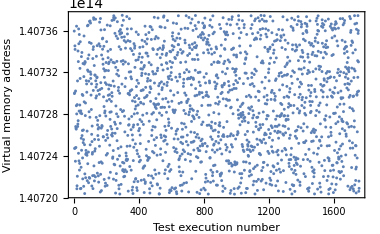

```mathematica
(* --- Statistical pattern of secret array memory locations --- *)
ListPlot[Flatten[spectreOutputLinuxSuccess],PlotRange->All,Ticks->All,PlotStyle->Thick,Frame->{True,True,False,False},FrameLabel->{"Test execution number","Virtual memory address"}]
```

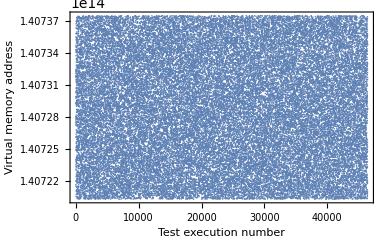

```mathematica
ListPlot[Flatten[spectreOutputLinuxFail],PlotRange->All,Ticks->All,Frame->{True,True,False,False},FrameLabel->{"Test execution number","Virtual memory address"}]
```

```mathematica
(* --- Statistical properties --- *)
NumberForm[N[Variance[spectreOutputLinuxSuccess]],50]
```

{2.41486222545742×10^19}

```mathematica
NumberForm[N[Variance[spectreOutputLinuxFail]],20]
```

{2.461335643164865×10^19}

```mathematica
NumberForm[N[Mean[spectreOutputLinuxSuccess]],20]
```

{1.40728958261518×10^14}

```mathematica
NumberForm[N[Mean[spectreOutputLinuxFail]],20]
```

{1.407288540051301×10^14}

```mathematica
(* Statistical tests *)
a1:=Min[Flatten[spectreOutputLinuxSuccess]]
a2:=Max[Flatten[spectreOutputLinuxSuccess]]
b1:=Min[Flatten[spectreOutputLinuxFail]]
b2:=Max[Flatten[spectreOutputLinuxFail]]

Mean[UniformDistribution[{a1,a2}]]
```

140728906636100

```mathematica
Mean[UniformDistribution[{b1,b2}]]
```

140728898204068

```mathematica
A:=DistributionFitTest[Flatten[spectreOutputLinuxSuccess], UniformDistribution[{a1,a2}],"HypothesisTestData"]
B:=DistributionFitTest[Flatten[spectreOutputLinuxFail], UniformDistribution[{b1,b2}],"HypothesisTestData"]
```

```mathematica
A["TestDataTable",All]
B["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 2.4376 | 0.0534353
Cramér-von Mises | 0.0645822 | 0.785178
Distance-to-Boundary | 0.0219822 | 0.36037
Kolmogorov-Smirnov | 0.0139859 | 0.878091
Kuiper | 0.0252487 | 0.701976
Pearson χ^2 | 33.0365 | 0.737776
Watson U^2 | 0.0486969 | 0.722123

| Statistic | P-Value
Anderson-Darling | 3.94214 | 0.00930431
Cramér-von Mises | 0.391737 | 0.0759785
Distance-to-Boundary | 0.00284229 | 0.847314
Pearson χ^2 | 136.778 | 0.71616

```mathematica
(* --- Total success rate --- *)
N[Length[spectreOutputLinuxSuccess]/(Length[spectreOutputLinuxSuccess]+Length[spectreOutputLinuxFail])] * 100
```

3.63561

```mathematica
For [i = 1, i < 30+1, ++i, spectreOutputNLinuxFail[i]=Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output/csv/spectre-output-"
<> ToString[i] <> "-fail-csv", "CSV"]]
```

```mathematica
For [i = 1, i < 30+1, ++i, spectreOutputNLinuxSuccess[i]=Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output/csv/spectre-output-"
<> ToString[i] <> "-success-csv", "CSV"]]
```

```mathematica
(* --- Individual success rates --- *)
For [i = 1, i < 30+1, ++i,
Print[N[Length[spectreOutputNLinuxSuccess[i]]/(Length[spectreOutputNLinuxSuccess[i]]+Length[spectreOutputNLinuxFail[i]])] * 100]]
```

2.01689

7.95276

0.578292

2.01207

1.36778

2.56709

1.93199

2.46

3.22581

4.52092

4.3038

2.96578

2.89063

6.20737

1.59176

1.25821

1.8574

5.37913

3.55951

3.70066

2.20769

2.87456

1.03921

5.90951

2.60926

7.13776

9.84991

8.413

11.0883

5.45159

```mathematica
(* --- Rust Spectre Mac OS Analysis --- *)
```

```mathematica
(* Unlocked desktop *)
spectreOutputMacUnlockedSuccess := Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/test-output-success-csv", "CSV"]
spectreOutputMacUnlockedFail:= Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/test-output-fail-csv", "CSV"]
(* Locked desktop *)
spectreOutputMacLockedSuccess := Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/test-output-locked-success-csv", "CSV"]
spectreOutputMacLockedFail:= Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/test-output-locked-fail-csv", "CSV"]
```

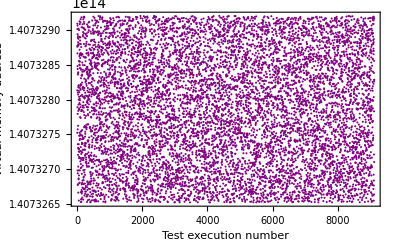

```mathematica
(* --- Statistical pattern of secret array memory locations --- *)
(* Unlocked desktop *)
ListPlot[Flatten[spectreOutputMacUnlockedSuccess],PlotRange->All,Ticks->All,PlotStyle->Purple,Frame->{True,True,False,False},FrameLabel->{"Test execution number","Virtual memory address"}]
```

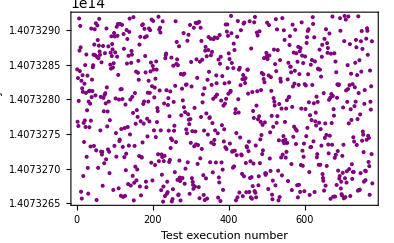

```mathematica
ListPlot[Flatten[spectreOutputMacUnlockedFail],PlotRange->All,Ticks->All,PlotStyle->Purple,Frame->{True,True,False,False},FrameLabel->{"Test execution number","Virtual memory address"}]
```

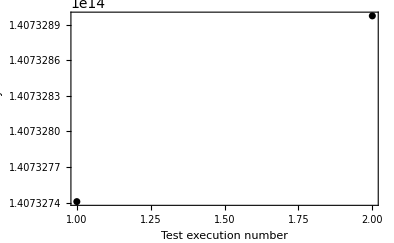

```mathematica
(* Locked desktop *)
ListPlot[Flatten[spectreOutputMacLockedSuccess],PlotRange->All,Ticks->All,PlotStyle->{Black,Thick},Frame->{True,True,False,False},FrameLabel->{"Test execution number","Virtual memory address"}]
```

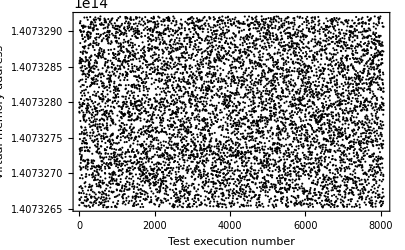

```mathematica
ListPlot[Flatten[spectreOutputMacLockedFail],PlotRange->All,Ticks->All,PlotStyle->Black,Frame->{True,True,False,False},FrameLabel->{"Test execution number","Virtual memory address"}]
```

```mathematica
(* --- Statistical properties --- *)
NumberForm[N[Variance[spectreOutputMacUnlockedSuccess]],20]
NumberForm[N[Variance[spectreOutputMacUnlockedFail]],20]
NumberForm[N[Variance[spectreOutputMacLockedSuccess]],20]
NumberForm[N[Variance[spectreOutputMacLockedFail]],20]
```

{6.003284603828249×10^15}

{6.09439928462888×10^15}

{1.228717987935027×10^16}

{5.931465782573973×10^15}

```mathematica
NumberForm[N[Mean[spectreOutputMacUnlockedSuccess]],20]
NumberForm[N[Mean[spectreOutputMacUnlockedFail]],20]
NumberForm[N[Mean[spectreOutputMacLockedSuccess]],20]
NumberForm[N[Mean[spectreOutputMacLockedFail]],20]
```

{1.407327860916937×10^14}

{1.40732786181864×10^14}

{1.40732819157428×10^14}

{1.40732787219181×10^14}

```mathematica
(* Statistical tests *)
z1:=Min[Flatten[spectreOutputMacUnlockedSuccess]]
z2:=Max[Flatten[spectreOutputMacUnlockedSuccess]]
w1:=Min[Flatten[spectreOutputMacUnlockedFail]]
w2:=Max[Flatten[spectreOutputMacUnlockedFail]]

x1:=Min[Flatten[spectreOutputMacLockedSuccess]]
x2:=Max[Flatten[spectreOutputMacLockedSuccess]]
y1:=Min[Flatten[spectreOutputMacLockedFail]]
y2:=Max[Flatten[spectreOutputMacLockedFail]]

Mean[UniformDistribution[{z1,z2}]]
Mean[UniformDistribution[{w1,w2}]]

Mean[UniformDistribution[{x1,x2}]]
Mean[UniformDistribution[{y1,y2}]]
```

140732786420148

140732786211252

140732819157428

140732786479540

```mathematica
X:=DistributionFitTest[Flatten[spectreOutputMacUnlockedSuccess], UniformDistribution[{z1,z2}],"HypothesisTestData"]
Y:=DistributionFitTest[Flatten[spectreOutputMacUnlockedFail], UniformDistribution[{w1,w2}],"HypothesisTestData"]
Z:=DistributionFitTest[Flatten[spectreOutputMacLockedSuccess], UniformDistribution[{x1,x2}],"HypothesisTestData"]
W:=DistributionFitTest[Flatten[spectreOutputMacLockedFail], UniformDistribution[{y1,y2}],"HypothesisTestData"]
```

```mathematica
X["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 2.27322 | 0.0653147
Cramér-von Mises | 0.0403407 | 0.931384
Distance-to-Boundary | 0.00577879 | 0.920929
Pearson χ^2 | 61.9451 | 0.877789

```mathematica
Y["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 2.31794 | 0.0618394
Cramér-von Mises | 0.0411198 | 0.92729
Distance-to-Boundary | 0.0184059 | 0.950319
Pearson χ^2 | 16.356 | 0.960249

```mathematica
(* Leave out - only 2 values: Z["TestDataTable",All] *)
```

```mathematica
W["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 3.08807 | 0.0246943
Cramér-von Mises | 0.132739 | 0.446735
Distance-to-Boundary | 0.0094247 | 0.469541
Pearson χ^2 | 51.0186 | 0.976476

```mathematica
(* --- Total success rate --- *)
(* Unlocked desktop *)
N[Length[spectreOutputMacUnlockedSuccess]/(Length[spectreOutputMacUnlockedSuccess]+Length[spectreOutputMacUnlockedFail])] * 100
(* Locked desktop *)
N[Length[spectreOutputMacLockedSuccess]/(Length[spectreOutputMacLockedSuccess]+Length[spectreOutputMacLockedFail])] * 100
```

92.1398

0.0247433

```mathematica
(* --- Individual success rates --- *)
(* Unlocked desktop *)
For [i = 1, i < 15+1, ++i,
spectreOutputNMacUnlockedSuccess[i]=Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/csv/spectre-output-"
<> ToString[i] <> "-success-csv", "CSV"]]
```

```mathematica
For [i = 1, i < 15+1, ++i, spectreOutputNMacUnlockedFail[i]=Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/csv/spectre-output-"
<> ToString[i] <> "-fail-csv", "CSV"]]
```

```mathematica
(* Locked desktop *)
```

```mathematica
(* Heuristic correction of no results *)
For [i = 1, i < 15+1, ++i,
spectreOutputNMacLockedSuccess[i]={}]
```

```mathematica
spectreOutputNMacLockedSuccess[1]=Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/csv/spectre-output-locked-1-success-csv", "CSV"];
spectreOutputNMacLockedSuccess[11]=Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/csv/spectre-output-locked-11-success-csv", "CSV"];

For [i = 1, i < 15+1, ++i,spectreOutputNMacLockedFail[i]=Import["/home/movrsprbp/idea-projects/spectre/target/debug/test-output-mac/csv/spectre-output-locked-"
<> ToString[i] <> "-fail-csv", "CSV"]]
```

```mathematica
For [i = 1, i < 15+1, ++i,
Print[N[Length[spectreOutputNMacUnlockedSuccess[i]]/(Length[spectreOutputNMacUnlockedSuccess[i]]+Length[spectreOutputNMacUnlockedFail[i]])] * 100]]
```

93.9394

88.3382

95.8651

90.0783

86.9898

96.2189

93.5196

65.8947

91.4355

92.4453

94.1341

93.9005

92.5926

92.4603

96.1655

```mathematica
For [i = 1, i < 15+1, ++i,
Print[N[Length[spectreOutputNMacLockedSuccess[i]]/(Length[spectreOutputNMacLockedSuccess[i]]+Length[spectreOutputNMacLockedFail[i]])] * 100]]
```

0.175747

0.

0.

0.

«6 more identical outputs»

0.364964

0.

0.

0.

«1 more identical outputs»

```mathematica
For [i = 1, i < 15+1, ++i,
Print[N[(Length[spectreOutputNMacUnlockedSuccess[i]]+Length[spectreOutputNMacUnlockedFail[i]])] ]]
```

726.

343.

919.

383.

392.

1005.

895.

475.

829.

503.

716.

623.

594.

504.

991.

```mathematica
For [i = 1, i < 15+1, ++i,
Print[N[(Length[spectreOutputNMacLockedSuccess[i]]+Length[spectreOutputNMacLockedFail[i]])] ]]
```

569.

476.

554.

909.

539.

468.

865.

259.

354.

386.

274.

548.

240.

800.

842.

```mathematica
For [i = 1, i < 30+1, ++i,
Print[N[(Length[spectreOutputNLinuxSuccess[i]]+Length[spectreOutputNLinuxFail[i]])]]]
```

2132.

1270.

2248.

1491.

1974.

1714.

1294.

5000.

1891.

1482.

1580.

1315.

1280.

1466.

1068.

1828.

1669.

1543.

899.

1216.

1223.

1148.

2117.

1083.

1533.

1401.

1066.

1569.

1461.

1229.